```mathematica
Length[deps3]
```

2436995

```mathematica
tokitok=Monitor[
Map[#[[2]]&,
Select[
Table[
With[{record=deps3[[k]]},
With[
{g=MyEdgeDelete[ReadGrof[record[[1]]],record[[3,3]]]},
{ReportOnMatrix[GenMatrix[g,record[[3,2]]]], record}
]
],
{k,2436995-10000,2436995}
],
#[[1]]=={2,1,2,2,3,5}&
]
],
k]
```

$Aborted

```mathematica
LinearEdges[vertices_]:=Table[vertices[[i]]<->vertices[[i+1]],{i,1,Length[vertices]-1}]
```

```mathematica
ShortestPaths[g_,vertices_]:=DeleteDuplicates[
Map[Sort[#]&,
Flatten[
Map[LinearEdges[#]&,
Select[
Flatten[Table[FindShortestPath[g,e1,e2],{e1,vertices},{e2,vertices}],1],
Length[#]>1&
]
]
]
]
]
```

```mathematica
DeleteDuplicates[tokitok,#1[[1]]==#2[[1]]&]
```

{{58681,390825,{3,{2,7,1,3,5},{5<->7,3<->7},{{2,5,7},{3,5,7},{1,3,7}}}},{58682,254750,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58683,254754,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58684,254774,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58685,254778,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58686,254780,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58687,254836,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58688,255193,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58690,255386,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58691,255392,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58692,255457,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58693,255601,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58701,264038,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58694,255607,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58695,255609,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58696,255665,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58697,257471,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58698,262496,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58699,262499,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58700,262530,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58702,264041,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58703,264043,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58704,264078,{3,{5,3,6,9,4},{3<->4,3<->9},{{3,4,5},{3,4,9},{3,6,9}}}},{58708,386693,{3,{5,3,8,6,4},{3<->4,3<->6},{{3,4,5},{3,4,6},{3,6,8}}}},{58709,386700,{3,{5,3,8,6,4},{3<->4,3<->6},{{3,4,5},{3,4,6},{3,6,8}}}},{58710,386696,{3,{5,3,8,6,4},{3<->4,3<->6},{{3,4,5},{3,4,6},{3,6,8}}}},{58711,387229,{3,{5,3,8,6,4},{3<->4,3<->6},{{3,4,5},{3,4,6},{3,6,8}}}},{58713,388986,{3,{5,3,8,6,4},{3<->4,3<->6},{{3,4,5},{3,4,6},{3,6,8}}}},{58716,398406,{3,{1,2,3,13,5},{2<->5,2<->13},{{1,2,5},{2,5,13},{2,3,13}}}}}

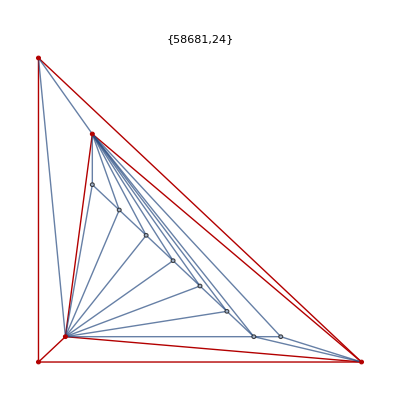
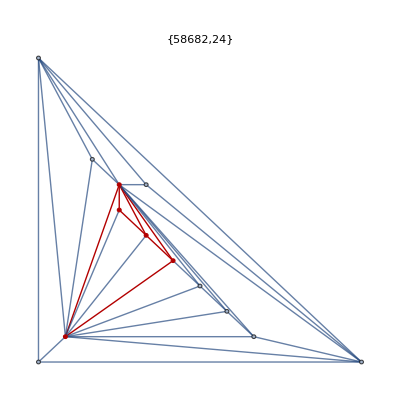
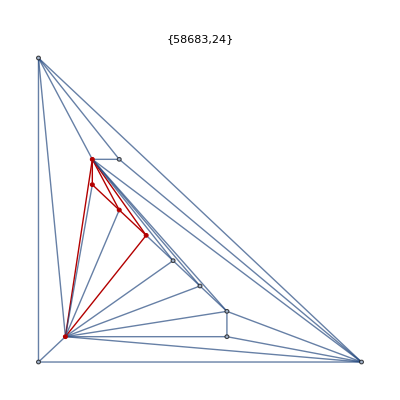
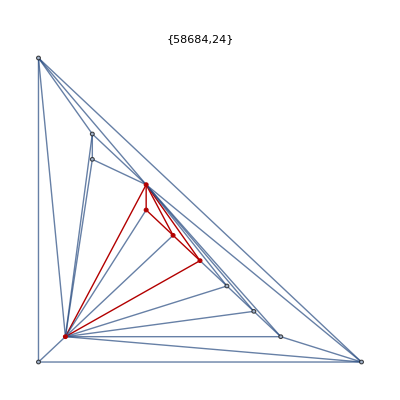
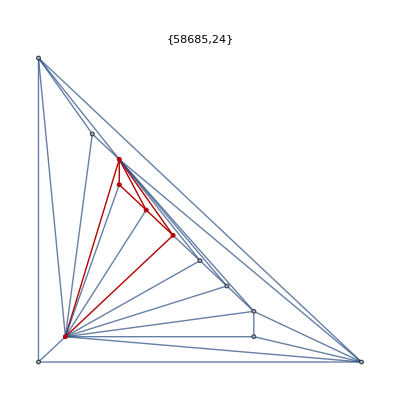
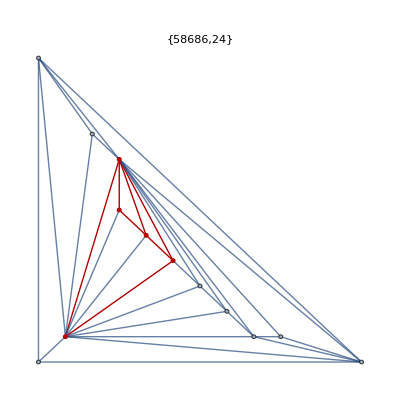
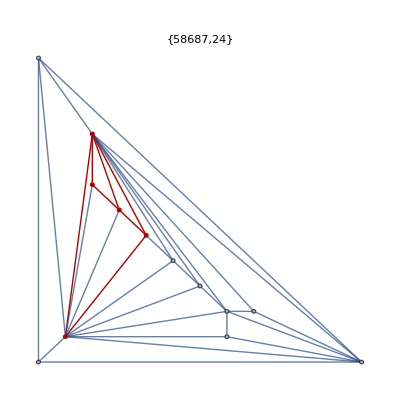
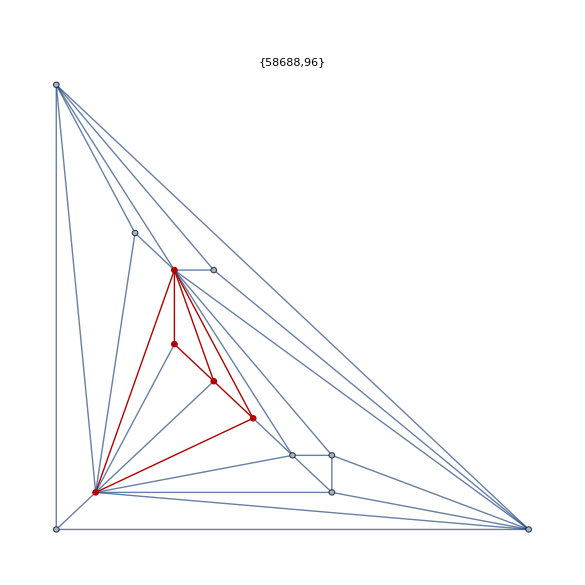

```mathematica
Map[
With[
{g=ReadGrof[#[[1]]], vertices=#[[3,2]]},
With[
{h=MyEdgeDelete[g,#[[3,3]]]},
Graph[g,
GraphLayout->"PlanarEmbedding", 
GraphHighlight->Join[vertices,ShortestPaths[h,vertices]],
PlotLabel->{#[[1]],Chrom[#[[1]]]}
]
]
]&
, DeleteDuplicates[tokitok,#1[[1]]==#2[[1]]&]
]
```

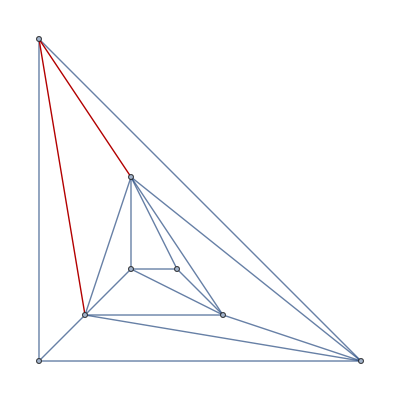

```mathematica
Graph[ReadGrof[10],GraphLayout->"PlanarEmbedding", GraphHighlight->{5<->7,3<->7}]
```

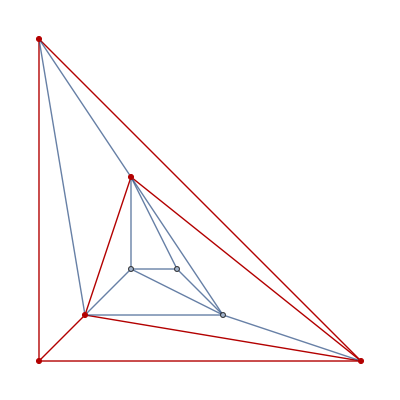

```mathematica
Graph[ReadGrof[10],GraphLayout->"PlanarEmbedding", GraphHighlight->{2,7,1,3,5,2<->7,1<->2,2<->3,2<->5,1<->7,1<->3,3<->5}]
```